## Convergencia numérica

```mathematica
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

ScheduledTaskObject[…]

## Paquetes a importar

```mathematica
Needs["MaTeX`"] (*Importa la paquetería de LaTeX*)
SetOptions[MaTeX, "Preamble" -> {"\\usepackage{xcolor}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
(*Directorio donde están las paqueterías*)
SetDirectory["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Programas\\Packages"]

Needs["MieTheory`"]
```

C:\Users\danal\Documents\Github\Tesis-de-Licenciatura\Programas\Packages

```mathematica
<< "MieTheory.wl"
```

## Definiciones

```mathematica
h=4.135667696*10^(-15); (*eV s*) (*Constante de Planck*)
hbar=6.582119569*10^(-16); (*eV s*)(*Constante de Planck reducida*)
c=299792458*^9 (*nm s^-1*)(*Velocidad de la luz*);

omega10=Range[0,10,0.01]; 
omegaVis=Range[2,3.1,0.01];
energyTicksMajorVisible={2.07,2.26,2.48,2.76,3.1};

epsPlasma=1.823;


(*Colores*)
blueUNAM=RGBColor[6/255,151/255,213/255];
redUNAM=RGBColor[232/255,68/255,42/255];
gris=RGBColor[127/255,146/255,151/255];
colors2={blueUNAM, redUNAM}
color5={Orange}
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x)
rojos=Table[RGBColor[1,g,0],{g,0,0.9,0.16}]
sunsetColors=Table[ColorData["SunsetColors"][i],{i,0,0.8,1/7}]
solarColors=Table[ColorData["SolarColors"][i],{i,0,0.8,1/7}]
alpineColors=Table[ColorData["AlpineColors"][i],{i,0,0.8,1/7}]
lakeColors=Table[ColorData["LakeColors"][i],{i,0,0.8,1/7}]
candyColors=Table[ColorData["CandyColors"][i],{i,0,0.8,1/7}]
verde=RGBColor[150/255,200/255,60/255]
```

{RGBColor[Rational[2, 85], Rational[151, 255], Rational[71, 85]],RGBColor[Rational[232, 255], Rational[4, 15], Rational[14, 85]]}

{RGBColor[1, 0.5, 0]}

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

{RGBColor[1, 0., 0],RGBColor[1, 0.16, 0],RGBColor[1, 0.32, 0],RGBColor[1, 0.48, 0],RGBColor[1, 0.64, 0],RGBColor[1, 0.8, 0]}

{RGBColor[0., 0., 0.],RGBColor[0.3195368571428571, 0.1164, 0.4341454285714286],RGBColor[0.6695744285714286, 0.22438285714285713, 0.338128],RGBColor[0.8974812857142858, 0.3693308571428571, 0.1452665142857143],RGBColor[0.9882154285714286, 0.5505617142857143, 0.08483494285714285],RGBColor[1., 0.7397017142857143, 0.23300614285714283]}

{RGBColor[0.468742, 0., 0.0158236],RGBColor[0.6706774285714285, 0.06984285714285714, 0.009042057142857144],RGBColor[0.8432481428571429, 0.15849014285714286, 0.008003357142857142],RGBColor[0.9277247142857143, 0.30355071428571423, 0.024193185714285713],RGBColor[0.978545, 0.4534661428571428, 0.0459689],RGBColor[0.995709, 0.6082364285714286, 0.07333049999999999]}

{RGBColor[0.277546, 0.355398, 0.484215],RGBColor[0.3092687142857143, 0.43180485714285716, 0.45451742857142857],RGBColor[0.35382528571428573, 0.4807017142857143, 0.3698534285714286],RGBColor[0.43932542857142853, 0.5335538571428571, 0.38461414285714285],RGBColor[0.5610134285714286, 0.5994675714285714, 0.49026099999999995],RGBColor[0.6995328571428572, 0.6994642857142856, 0.6226554285714285]}

{RGBColor[0.293416, 0.0574044, 0.529412],RGBColor[0.40930385714285716, 0.25890179999999996, 0.6923064285714285],RGBColor[0.5251917142857143, 0.46039919999999995, 0.8552008571428571],RGBColor[0.6206238571428572, 0.6188315714285714, 0.9107938571428571],RGBColor[0.7058281428571428, 0.7557314285714285, 0.9127361428571429],RGBColor[0.7881374285714285, 0.8555037142857143, 0.9026041428571429]}

{RGBColor[0.405188, 0.204349, 0.343389],RGBColor[0.6033010000000001, 0.22473442857142858, 0.36270257142857143],RGBColor[0.7647998571428571, 0.3022755714285714, 0.4413708571428571],RGBColor[0.8306595714285715, 0.45290014285714286, 0.5840857142857143],RGBColor[0.7940618571428572, 0.5946167142857143, 0.7287942857142857],RGBColor[0.7161124285714285, 0.7039788571428571, 0.8368194285714285]}

RGBColor[Rational[10, 17], Rational[40, 51], Rational[4, 17]]

## Funciones

```mathematica
dataQext[dataCabs_,dataCsca_]:=Module[{dataCext},
dataCext=Transpose[{dataCabs[[All,1]],dataCabs[[All,2]]+dataCsca[[All,2]]}]]

errorAbs[data1_,data2_]:=Module[{error},
error=Abs[data1-data2]]

errorRel[data1_,data2_]:=Module[{error},
error=100*Abs[data1-data2]/data2]
```

## Gráficas

```mathematica
plotStyling = {PlotRange -> All,
   PlotStyle -> (Directive[#, Thickness[0.003]] & /@ sunsetColors),  
   Frame -> True,
   FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
   LabelStyle->{FontFamily->"Latin Modern Roman 10"},
   ImagePadding->{{90,10},{60,60}}};
  
  
  SetDirectory["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Figuras\\4-Resultados"]
```

C:\Users\danal\Documents\Github\Tesis-de-Licenciatura\Figuras\3-FIT

## Eritrocito sano

```mathematica
dataEriSanoCabs=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Eritrocito_sano_Cabs_12_11_10.csv"];
dataEriSanoCsca=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Eritrocito_sano_Csca_12_11_10.csv"];

dataQabsEriSano=Transpose[{dataEriSanoCabs[[All,1]],dataEriSanoCabs[[All,#]]/(Pi*2680^2)}]&/@Range[2,4];
dataQscaEriSano=Transpose[{dataEriSanoCsca[[All,1]],dataEriSanoCsca[[All,#]]/(Pi*2680^2)}]&/@Range[2,4];
```

```mathematica
hola=Interpolation[Transpose[{dataEriSanoCabs[[All,1]],dataQext[dataQabsEriSano[[3]],dataQscaEriSano[[3]]][[All,2]]}]]
```

InterpolatingFunction[…]

```mathematica
MinimalBy[Table[{x,hola[x]},{x,430,450}],Last]
```

{{440,1.46738}}

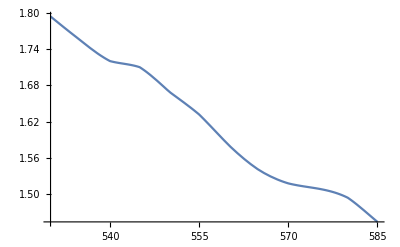

```mathematica
Plot[hola[x],{x,530,585}]
```

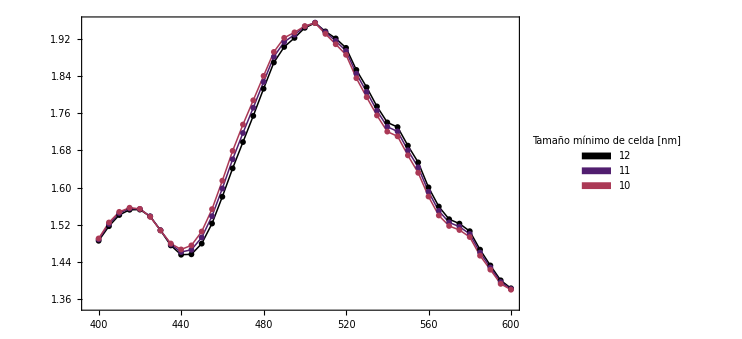

```mathematica
plotEriSano=ListPlot[dataQext[dataQabsEriSano[[#]],dataQscaEriSano[[#]]]&/@Range[1,3],PlotMarkers->{"●",6},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"12","11","10"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",2},
                                    LegendMargins->0,
                                    LegendLabel->Style["Tamaño mínimo de celda [nm]",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.5,0.2}],
                      Joined->True,
                      PlotStyle -> (Directive[#, Thickness[0.002]] & /@ sunsetColors),
                      Evaluate[Sequence @@ plotStyling]]
```

## Esferocito

```mathematica
dataEsfCabs=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Esferocito_Cabs_12_11_10.csv"];
dataEsfCsca=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Esferocito_Csca_12_11_10.csv"];

dataQabsEsf=Transpose[{dataEsfCabs[[All,1]],dataEsfCabs[[All,#]]/(Pi*2680^2)}]&/@Range[2,4];
dataQscaEsf=Transpose[{dataEsfCsca[[All,1]],dataEsfCsca[[All,#]]/(Pi*2680^2)}]&/@Range[2,4];
```

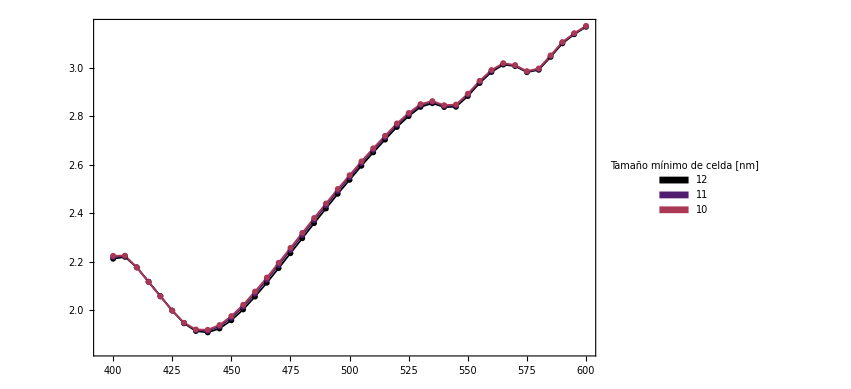

```mathematica
plotEsferocito=ListPlot[dataQext[dataQabsEsf[[#]],dataQscaEsf[[#]]]&/@Range[1,3],PlotMarkers->{"●",6},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"12","11","10"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",2},
                                    LegendMargins->0,
                                    LegendLabel->Style["Tamaño mínimo de celda [nm]",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.5,0.2}],
                      Joined->True,
                      PlotStyle -> (Directive[#, Thickness[0.002]] & /@ sunsetColors),
                      Evaluate[Sequence @@ plotStyling]]
```

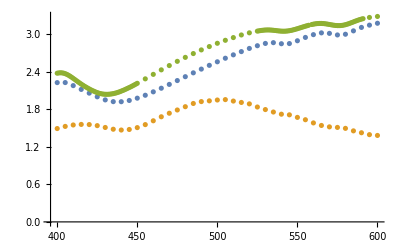

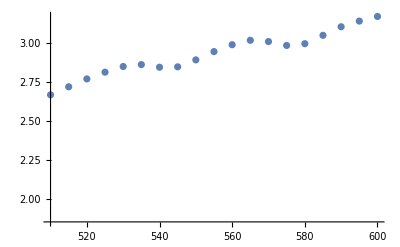

```mathematica
ListPlot[{dataQext[dataQabsEsf[[3]],dataQscaEsf[[3]]],dataQext[dataQabsEriSano[[3]],dataQscaEriSano[[3]]],dataQext[dataQabsMeshLocal[[3]],dataQscaMeshLocal[[3]]]}]
ListPlot[{dataQext[dataQabsEsf[[3]],dataQscaEsf[[3]]]},PlotRange->{{510,600},{Automatic,Automatic}}]
```

```mathematica
dataQext[dataQabsEsf[[3]],dataQscaEsf[[3]]]
```

{{400,2.22487},{405,2.22549},{410,2.17673},{415,2.11611},{420,2.0567},{425,1.99797},{430,1.94863},{435,1.92089},{440,1.9197},{445,1.9394},{450,1.97624},{455,2.02278},{460,2.07737},{465,2.13518},{470,2.19612},{475,2.25751},{480,2.31929},{485,2.38075},{490,2.44059},{495,2.50055},{500,2.55721},{505,2.61427},{510,2.66817},{515,2.72},{520,2.77078},{525,2.81391},{530,2.85048},{535,2.86288},{540,2.84589},{545,2.84847},{550,2.89316},{555,2.94649},{560,2.99087},{565,3.01918},{570,3.01117},{575,2.98614},{580,2.99743},{585,3.0513},{590,3.10635},{595,3.14286},{600,3.17274}}

```mathematica
MinimalBy[dataQext[dataQabsEriSano[[3]],dataQscaEriSano[[3]]],Last]
```

{{600,1.38098}}

## Microcito

## Macrocito